```mathematica
(* Ferroelectric Work Including the deformation of the unit cell arising from strain about the phase transition temperature *)

Needs["VariationalMethods`"]
Clear["`*"]
Symbol[ "a1"]Symbol[ "a11"]Symbol[ "a12"]Symbol[ "a111"]Symbol[ "a112"]Symbol[ "a123"]Symbol[ "a1111"]Symbol[ "a1112"]Symbol[ "a1122"]Symbol["a1123"];
Symbol["T"]Symbol["σ"]Symbol["s"]Symbol["Q"];
Symbol["P"]; Symbol["u"]; Symbol["α"] Symbol["q"];
Symbol[ "a"] Symbol["g"] Symbol["x"] Symbol["ϕ"] Symbol["ψ"] Symbol["γ"];
Symbol["b"] Symbol["Ps"];
Symbol["u1"]Symbol["u2"]Symbol["u3"]Symbol["u4"]Symbol["u5"]Symbol["u6"];

P[x_]={0,0,P3[x]};
PGrad={PG11,PG22,PG33,PG23,PG13,PG12, PG32, PG31, PG21};
(* x={x1,x2,x3}; *)
u={0,0,u3,0,0,0};

ϕ={0,0,0};

FPolar[P_]=a1(Indexed[P[x],1]^2+Indexed[P[x],2]^2+Indexed[P[x],3]^2)+a11(Indexed[P[x],1]^4+Indexed[P[x],2]^4+Indexed[P[x],3]^4)+a12(Indexed[P[x],1]^2*Indexed[P[x],2]^2+Indexed[P[x],2]^2*Indexed[P[x],3]^2+Indexed[P[x],1]^2*Indexed[P[x],3]^2);

FGradient[P_]=g11/2*(Indexed[PGrad,1]^2  +Indexed[PGrad,2]^2+Indexed[PGrad,3]^2)+
g12*(Indexed[PGrad, 2]Indexed[PGrad, 3]+Indexed[PGrad, 1]Indexed[PGrad, 3]+Indexed[PGrad, 1]Indexed[PGrad, 2])+g44/2*((Indexed[PGrad, 6]+Indexed[PGrad, 9])^2+(Indexed[PGrad, 4]+Indexed[PGrad, 7])^2+(Indexed[PGrad, 8]+Indexed[PGrad, 5])^2);
(* + Indexed[ν, {i,j,k,l}]/2*(Indexed[ϕ,{i,","j}]Indexed[ϕ,{k,","l}])+
Indexed[w, {i,j,k,l}]/2*(Indexed[ψ,{i,","j}]Indexed[ψ,{k,","l}])   *)

D[FPolar[P], Indexed[P,1]];
D[FGradient[P], PG11];

FElectrostriction[P_,u_]=-q11*(Indexed[u,1]*Indexed[P[x],1]^2+Indexed[u,2]*Indexed[P[x],2]^2+Indexed[u,3]*Indexed[P[x],3]^2)-q12*(Indexed[u,1]*(Indexed[P[x],2]^2+Indexed[P[x],3]^2)+Indexed[u,2]*(Indexed[P[x],1]^2+Indexed[P[x],3]^2)+Indexed[u,3]*(Indexed[P[x],1]^2+Indexed[P[x],2]^2))-
q44*(Indexed[u,6]*(Indexed[P[x],1]*Indexed[P[x],2])+Indexed[u,5]*(Indexed[P[x],1]*Indexed[P[x],3])+Indexed[u,4]*(Indexed[P[x],2]*Indexed[P[x],3]));
FElastic[u_]=1/2*c11*(Indexed[u,1]^2+Indexed[u,2]^2+Indexed[u,3]^2)+c12*(Indexed[u,2]*Indexed[u,3]+Indexed[u,1]*Indexed[u,3]+Indexed[u,1]*Indexed[u,2])+1/2*c44*(Indexed[u,4]^2+Indexed[u,5]^2+Indexed[u,6]^2);
FStructural[ϕ_]=b1 (Indexed[ϕ,1]^2+Indexed[ϕ,2]^2+Indexed[ϕ,3]^2)+b11(Indexed[ϕ,1]^4+Indexed[ϕ,2]^4+Indexed[ϕ,3]^4)+b12(Indexed[ϕ,1]^2*Indexed[ϕ,2]^2+Indexed[ϕ,2]^2*Indexed[ϕ,3]^2+Indexed[ϕ,2]^2*Indexed[ϕ,3]^2);

FBiquadraticCoupling[P_,ϕ_]=-t11(Indexed[ϕ,1]^2*Indexed[P,1]^2+Indexed[ϕ,2]^2*Indexed[P,2]^2+Indexed[ϕ,3]^2*Indexed[P,3]^2)-t12*(Indexed[ϕ,1]^2*(Indexed[P,2]^2+Indexed[P,3]^2)+Indexed[ϕ,2]^2*(Indexed[P,1]^2+Indexed[P,3]^2)+Indexed[ϕ,3]^2*(Indexed[P,1]^2+Indexed[P,2]^2))-t44(Indexed[ϕ,1]Indexed[ϕ,2]Indexed[P,1]Indexed[P,2]+Indexed[ϕ,2]Indexed[ϕ,3]Indexed[P,2]Indexed[P,3]+Indexed[ϕ,1]Indexed[ϕ,3]Indexed[P,1]Indexed[P,3])-
R11*(Indexed[u,1]*Indexed[ϕ,1]^2+Indexed[u,2]*Indexed[ϕ,2]^2+Indexed[u,3]*Indexed[ϕ,3]^2)-R12*(Indexed[u,1]*(Indexed[ϕ,2]^2+Indexed[ϕ,3]^2)+Indexed[u,2]*(Indexed[ϕ,1]^2+Indexed[ϕ,3]^2)+Indexed[u,3]*(Indexed[ϕ,1]^2+Indexed[ϕ,2]^2))-
R44*(Indexed[u,4]*Indexed[ϕ,2]*Indexed[ϕ,3]+Indexed[u,5]*Indexed[ϕ,1]*Indexed[ϕ,3]+Indexed[u,6]*Indexed[ϕ,1]*Indexed[ϕ,2]);

FBulk[P_,ϕ_,u_]=FPolar[P[x]]+FElectrostriction[P[x], u]+FElastic[u]+FStructural[ϕ]+FBiquadraticCoupling[P,ϕ];    (* + FGradient[P] *)
D[FBulk[P[x],ϕ,u],P3[x]];


(* Step 1. Solve for the strain relations in terms of the other order parameters and subtitute these solutions into the free energy. *)
y=Solve[{(D[FBulk[P[x],ϕ,u],u1])==0,(D[FBulk[P[x],ϕ,u],u2])==0, (D[FBulk[P[x],ϕ,u],u3])==0}, {u1, u2,u3}]
(* z=Solve[{(D[FBulk[P[x],ϕ,u],ϕ1])==0,(D[FBulk[P[x],ϕ,u],ϕ2])==0, (D[FBulk[P[x],ϕ,u],ϕ3])==0, ϕ1≠ 0, ϕ2≠0}, {ϕ1, ϕ2,ϕ3}]; *)
FBulkSolvedStrain[P_,ϕ_]=FBulk[P[x],ϕ,u]/.y[[1]]
(* FBulkSolvedStrainStructure[P_]=FBulk[P[x],ϕ,u]//.z[[4]]//.y[[1]]; *)
PSolution[x_]=Solve[D[FBulkSolvedStrain[P[x], ϕ],P3[x]]==0, P3[x]];

PSolution2=(P3[x]/.PSolution[x][[1]])^2;
FullSimplify[PSolution2//.{(c11+2 c12)-> A, (c11-c12)-> B, (2 b11+b12)-> H, (q11 R11+2 q12 R12)->J, (c11+c12) -> L}];
(* Future Work With Gradient Terms
 FullSimplify[DSolve[(D[FBulkSolvedStrain[P[x],ϕ],P3[x]])==g*P3''[x], P3[x],x]]
EulerEquations[FBulk[P[x],ϕ,u], P3[x],x];
DSolve[%, P[x], x];
*)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{u3→(q11 P3[x]^2)/c11}}

a1 P3[x]^2+a11 P3[x]^4-(q11^2 P3[x]^4)/(2 c11)

```mathematica
(* Solving the domain wall width for the tetragonal phase under simple strain conditions *)
 FullSimplify[DSolve[(D[FBulkSolvedStrain[P[x],ϕ],P3[x]])==g*P3''[x], P3[x],x]]
PSolution2=(P3[x]/.%[[1]])^2
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P3[x]→-(ⅈ JacobiSN[√(((2 a11 c11-q11^2) C[1] (x+C[2])^2)/(-a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))),(a1 c11-√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))/(a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))])/(√((-2 a11 c11+q11^2)/(-a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))))},{P3[x]→(ⅈ JacobiSN[√(((2 a11 c11-q11^2) C[1] (x+C[2])^2)/(-a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))),(a1 c11-√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))/(a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))])/(√((-2 a11 c11+q11^2)/(-a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))))}}

-((-a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1]))) JacobiSN[√(((2 a11 c11-q11^2) C[1] (x+C[2])^2)/(-a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))),(a1 c11-√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))/(a1 c11+√(c11 (a1^2 c11+g (2 a11 c11-q11^2) C[1])))]^2)/(-2 a11 c11+q11^2)

```mathematica
(* _____________________________________________________________________________________________________________________________________________________________________________*)

Clear["S", "L"]
(* S'=1/(a1 c11+√(c11 (a1^2 c11+g (-2 a11 c11+q11^2) C[1]))); S=(2 a11 c11-q11^2)/(a1 c11+√(c11 (a1^2 c11+g (-2 a11 c11+q11^2) C[1])))*)

SimplifiedPolarizationTetragonal[x_]=(ⅈ JacobiSN[√(-S* C[1] (x+C[2])^2),L])/S;

Limit[(ⅈ JacobiSN[(i*S*C[1]x)^(1/2),L])/S, x-> Infinity]

(* If the polarization goes to zero at the center of the domain wall, then the following equations can be utilized to solve for 
  constants of integratation. *)
Limit[SimplifiedPolarizationTetragonal[x], x-> 0];
JacobiSN[0,L];

(* Determines the domain wall width by analyzing the derivative and setting it equal to zero *)
D[(ⅈ JacobiSN[√(-S* C[1] x^2),L])/S, x];
Solve[%==0,x]


(* D[JacobiSN[(S)^(1/2),L], S]
Limit[(ⅈ C[1] (x+C[2]) JacobiCN[√(-S C[1] (x+C[2])^2),1] JacobiDN[√(-S C[1] (x+C[2])^2),1])/(√(-S C[1] (x+C[2])^2)), x->Infinity]

Limit[i*JacobiCN[√-Sx,1], x->Infinity]
FullSimplify[JacobiSN[ix,0]]
*)
```

Limit[(ⅈ JacobiSN[√(i S x C[1]),L])/S,x→∞]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-(ⅈ EllipticK[L])/(√S √C[1])},{x→-(ⅈ InverseJacobiDN[0,L])/(√S √C[1])}}

{1,2,3}

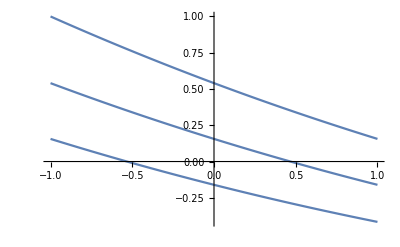

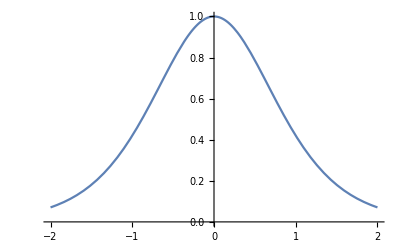

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* Plots of Jacobian Functions *)
a={1,2,3}
Plot[JacobiCN[(x+a)^(1/2),0],{x,-1,1}]
Plot[Sech[(x)]^2,{x,-2,2}]
Plot[InverseJacobiDN[0,1/2], {x, -5,5}]
```